```mathematica
data=Dataset[<|"p"-><|"r"->1,"s"->2,"t"->3|>,"q"-><|"r"->5,"s"->10,"t"->7|>|>]
```

```mathematica
data["p","s"]
```

2

```mathematica
data["p"]
```

```mathematica
data[All,"r"]
```

```mathematica
data[[All,"r"]]
```

```mathematica
data[f,"r"]
```

f[<|p→1,q→5|>]

```mathematica
data["q",f]
```

f[<|r→5,s→10,t→7|>]

```mathematica
data[All,f]
```

```mathematica
data[All,Total]
```

```mathematica
data[All,(#r+#t)&]
```

```mathematica
data[Select[#t>5&]]
```

```mathematica
data[SortBy[#r-#s&]]
```

```mathematica
data[All,#r+#s&]
```

```mathematica
data[All,PieChart]
```

```mathematica
data[All,BarChart]
```

```mathematica
data[All,PieChart3D]
```

```mathematica
data[All,BarChart3D]
```

```mathematica
data[All,PieChart[#,PlotTheme->"Business"]&]
```

```mathematica
data[f,"t"]
```

f[<|p→3,q→7|>]

```mathematica
data[f,Total]
```

f[<|p→6,q→22|>]

```mathematica
data[Max,Total]
```

22

```mathematica
data[All,Total]
```

```mathematica
data[All,Total]["q"]
```

22

```mathematica
data["q",Total]
```

22

```mathematica
data[Select[#t>5&]]
```

```mathematica
data[Select[#t>5&]]
```

```mathematica
data[All,Select[#>5&]]
```

```mathematica
Normal[data[All,Select[#>5&]]]
```

<|p→<||>,q→<|s→10,t→7|>|>

```mathematica
SortBy[Which[EvenQ[#],#,OddQ[#],10+#]&][{1,3,6,8,2,5,9,7}]
```

{2,6,8,1,3,5,7,9}

```mathematica
data[SortBy[#r-#s&]]
```

```mathematica
data[SortBy[#r-#s&],Total]
```

```mathematica
data[All,All,f]
```

```mathematica
data[SortBy[#r-#s&],Total,#^3&]
```

```mathematica
Dataset[{<|"p"->2,"q"->4,"r"->6|>,<|"p"->11,"q"->7,"r"->1|>}]
```

```mathematica
Dataset[{<|"p"->2,"q"->4,"r"->6|>,<|"p"->11,"q"->7|>}]
```

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

CloudConnect::clver: Connecting to a cloud running an earlier version of the Wolfram Engine: 13.1

```mathematica
planets[All,"Radius"]
```

```mathematica
planets[All,#Radius&]
```

```mathematica
planets[All,UnitConvert[#Radius]&]
```

```mathematica
planets[All,UnitConvert[#Radius,"Megameters"]&]
```

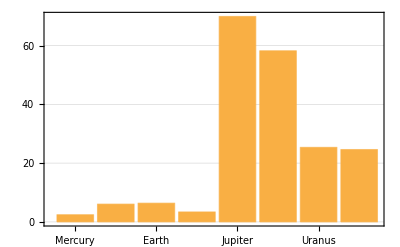

```mathematica
BarChart[planets[All,"Radius"],ChartLabels->Automatic,PlotTheme->"Business",TargetUnits->"Megameters"]
```

```mathematica
planets["Mars","Moons"]
```

```mathematica
planets["Mars","Moons",All,"Radius"]
```

```mathematica
planets["Mars","Moons",All,UnitConvert[#Radius,"Kilometers"]&]
```

```mathematica
planets[All,"Moons",Length]
```

```mathematica
planets[All,"Moons",Total,"Mass"]
```

```mathematica
planets[All,"Moons",Mean,"Mass"]
```

```mathematica
planets[All,"Moons",Median,"Mass"]
```

```mathematica
planets[All,"Moons",StandardDeviation,"Mass"]
```

```mathematica
planets[Select[Length[#Moons]>10&],"Moons",Total,"Mass"]
```

```mathematica
PieChart[planets[Select[Length[#Moons]>10&],"Moons",Total,"Mass"],ChartLegends->Automatic,PlotTheme->"Classic"]
```

-Graphics-

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]
```

```mathematica
Normal[planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]]
```

<|Mercury→{},Venus→{},Earth→{Moon},Mars→{},Jupiter→{Callisto,Ganymede,Io},Saturn→{Titan},Uranus→{},Neptune→{}|>

```mathematica
Catenate[Normal[planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]]]
```

{Moon,Callisto,Ganymede,Io,Titan}

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][Catenate,Keys]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][Catenate,Keys]//Normal
```

{Moon,Callisto,Ganymede,Io,Titan}

```mathematica
planets[All,"Moons",NumberLinePlot[Values[#]]&,Log[#Mass/Quantity[, "EarthMass"]]&]
```

```mathematica
planets["Mars","Moons"]
```

```mathematica
planets[All,"Moons",Total,"Mass"]
```

```mathematica
planets[All,"Moons",Select[#Mass>&]][All]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]
```

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Values]
```

```mathematica
Normal[planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]]
```

<|Mercury→{},Venus→{},Earth→{Moon},Mars→{},Jupiter→{Callisto,Ganymede,Io},Saturn→{Titan},Uranus→{},Neptune→{}|>

```mathematica
Catenate[Normal[planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Keys]]]
```

{Moon,Callisto,Ganymede,Io,Titan}

```mathematica
Catenate[Normal[planets[All,"Moons",Select[#Mass>Quantity[0.01, "EarthMass"]&]][All,Values]]]
```

{<|Mass→7.346×10^22 kg,Radius→1079.6 mi|>,<|Mass→1.076×10^23 kg,Radius→1497.7 mi|>,<|Mass→1.482×10^23 kg,Radius→1635. mi|>,<|Mass→8.93×10^22 kg,Radius→1131.9 mi|>,<|Mass→1.345×10^23 kg,Radius→1600.3 mi|>}

```mathematica
planets[All,"Moons",NumberLinePlot[Values[#]]&,Log[#Mass/Quantity[1,"Kilograms"]]&]
```

```mathematica
WordCloud[<|"P"->5,"Q"->7|>]
```

-Graphics-

```mathematica
planets[Association[Values[#]]&,"Moons",All,"Mass"]
```

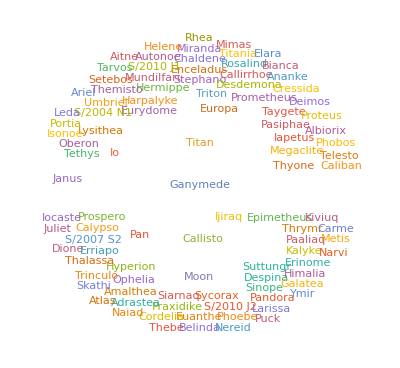

```mathematica
planets[WordCloud[Association[Values[#]]]&,"Moons",All,"Mass"]
```

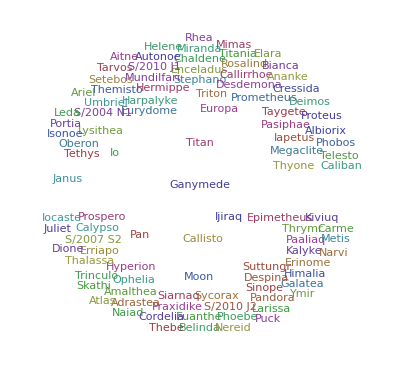

```mathematica
planets[WordCloud[Association[Values[#]],PlotTheme->"Classic"]&,"Moons",All,"Mass"]
```

```mathematica
p//q//r//s//t
```

t[s[r[q[p]]]]

```mathematica
(q/*r/*s/*t)[p]
```

t[s[r[q[p]]]]

```mathematica
p@q@r@s@t
```

p[q[r[s[t]]]]

```mathematica
(p@*q@*r@*s)[t]
```

p[q[r[s[t]]]]

```mathematica
WordCloud@*Association@*Values
```

WordCloud@*Association@*Values

```mathematica
planets[WordCloud@*Association@*Values,"Moons",All,"Mass"]
```

-Graphics-

```mathematica
planets[Values/*Association/*WordCloud,"Moons",All,"Mass"]
```

-Graphics-

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

```mathematica
GeoListPlot[fireballs[All,"Coordinates"]]
```

-Graphics-

```mathematica
GeoListPlot[fireballs[All,"Coordinates"],ImageSize->Full,GeoBackground->"VectorClassic"]
```

-Graphics-

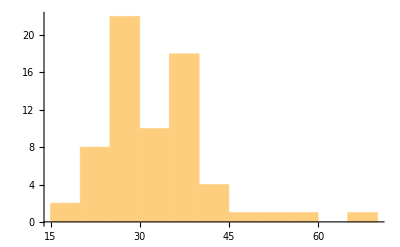

```mathematica
Histogram[fireballs[All,"Altitude"]]
```

```mathematica
planets[WordCloud@*Association@*Values,"Moons",All,"Mass"]
```

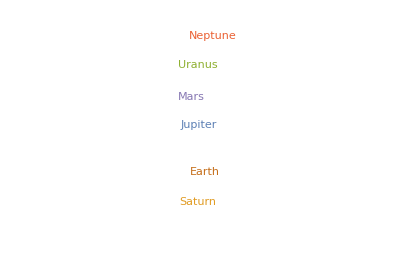

```mathematica
planets[WordCloud@*Association@*Values,"Moons",Length]
```

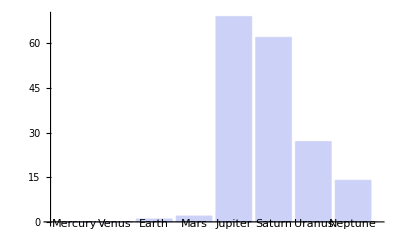

```mathematica
BarChart[planets[All,"Moons",Length],ImageSize->Full,PlotTheme->"Classic",ChartLabels->Automatic]
```

```mathematica
BarChart[planets[All,"Moons",Length],ImageSize->Full,PlotTheme->"Classic",ChartLabels->Automatic,TargetUnits->"Yottagrams"]
```

-Graphics-

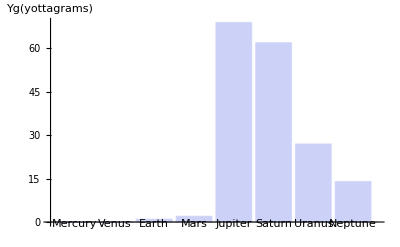

```mathematica
BarChart[planets[All,"Moons",Length],ImageSize->Full,PlotTheme->"Classic",ChartLabels->Automatic,TargetUnits->"Yottagrams",AxesLabel->{None,QuantityForm["Yottagrams",{"Abbreviation","LongForm"}]}]
```

```mathematica
data[SortBy[#r-#s&],Total]
```

```mathematica
data[SortBy[#r-#s&],Total,#^3&]
```

```mathematica
data[SortBy[#r-#s&],Total,#^(1/3)&]
```

```mathematica
planets[SortBy[Length[#Moons]&],"Mass"]
```

```mathematica
planets[All,"Moons",All,"Mass"]
```

```mathematica
planets[All,"Moons",Max,"Mass"]
```

```mathematica
Quantity[-∞,"Yottagrams"]
```

-∞ Yg

```mathematica
planets[All,"Moons",Max,Which[QuantityQ[#Mass],UnitConvert[#Mass,"Yottagrams"],!QuantityQ[#Mass],#Mass]&]
```

```mathematica
planets[All,"Moons"]
```

```mathematica
planets[SortBy[Length[#Moons]&],"Mass"]
```

```mathematica
planets[-1,Length[#Moons]&]
```

14

```mathematica
planets[-1,#Moons&]
```

```mathematica
planets[-1,Max[#Moons]&,All,"Mass"]
```

2.139×10^22 kg

```mathematica
planets[All,Max[#Moons]&,All,"Mass"]
```

Make a dataset of masses of planets, where the planets are sorted by the largest mass of their moons.

```mathematica
planets[All,Max[#Moons]&,All,"Mass"]
```

Make a dataset of masses of planets, where the planets are sorted by the largest mass of their moons.

```mathematica
planets[All,"Moons",All,f]
```

```mathematica
planets[All,"Moons",All,"Mass"]
```

```mathematica
planets["Mercury","Mass"]
```

3.30104×10^23 kg

```mathematica
planets[1;;3,"Mass"]
```

```mathematica
planets[1;;3,All]
```

```mathematica
planets[SortBy[#Mass&],"Mass"]
```

```mathematica
planets[All,"Moons"]
```

```mathematica
planets[All,"Moons",Length]
```

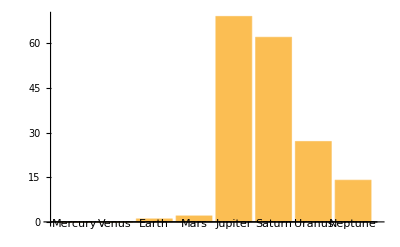

```mathematica
BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

All is descending.

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[0.01,"EarthMass"]&]][All,Keys]
```

SortBy is descending.

```mathematica
planets[All,"Moons",Values,Max[#Mass&]]
```

```mathematica
planets[All,All,f]
```

```mathematica
planets[All,"Moons",Which[Length[#]>2,TakeLargestBy[#Mass,1],Length[#]<=2,#]&]
```

Failure[…]

```mathematica
planets[All,f,All]
```

```mathematica
store=EntityStore[RelationalDatabase[FindFile["ExampleData/ecommerce-database.sqlite"]]]
```

EntityStore[…]

```mathematica
EntityRegister[store]
```

{orderdetails,productlines,payments,customers,employees,offices,products,orders}

```mathematica
EntityValue["offices","Dataset"]
```

```mathematica
EntityValue["offices",{"city","phone"},"Dataset"]
```

```mathematica
combined=CombinedEntityClass["customers","payments","customerNumber"]
```

CombinedEntityClass[customers,payments,customerNumber]

```mathematica
combined["Properties"]
```

{addressLine1,addressLine2,city,contactFirstName,contactLastName,country,creditLimit,customerName,customerNumber,employees,orders,payments,phone,postalCode,salesRepEmployeeNumber,state,amount,checkNumber,customerNumber,customers,paymentDate}

```mathematica
combined
```

CombinedEntityClass[customers,payments,customerNumber]

```mathematica
EntityList[combined]
```

{{103,103,HQ336336},{103,103,JM555205},{103,103,OM314933},{112,112,BO864823},{112,112,HQ55022},{112,112,ND748579},{114,114,GG31455},{114,114,MA765515},{114,114,NP603840},{114,114,NR27552},{119,119,DB933704},{119,119,LN373447},{119,119,NG94694},{121,121,DB889831},{121,121,FD317790},{121,121,KI831359},{121,121,MA302151},{124,124,AE215433},{124,124,BG255406},{124,124,CQ287967},{124,124,ET64396},{124,124,HI366474},{124,124,HR86578},{124,124,KI131716},{124,124,LF217299},{124,124,NT141748},{128,128,DI925118},{128,128,FA465482},{128,128,FH668230},{128,128,IP383901},{129,129,DM826140},{129,129,ID449593},{129,129,PI42991},{131,131,CL442705},{131,131,MA724562},{131,131,NB445135},{141,141,AU364101},{141,141,DB583216},{141,141,DL460618},{141,141,HJ32686},{141,141,ID10962},{141,141,IN446258},{141,141,JE105477},{141,141,JN355280},{141,141,JN722010},{141,141,KT52578},{141,141,MC46946},{141,141,MF629602},{141,141,NU627706},{144,144,IR846303},{144,144,LA685678},{145,145,CN328545},{145,145,ED39322},{145,145,HR182688},{145,145,JJ246391},{146,146,FP549817},{146,146,FU793410},{146,146,LJ160635},{148,148,BI507030},{148,148,DD635282},{148,148,KM172879},{148,148,ME497970},{151,151,BF686658},{151,151,GB852215},{151,151,IP568906},{151,151,KI884577},{157,157,HI618861},{157,157,NN711988},{161,161,BR352384},{161,161,BR478494},{161,161,KG644125},{161,161,NI908214},{166,166,BQ327613},{166,166,DC979307},{166,166,LA318629},{167,167,ED743615},{167,167,GN228846},{171,171,GB878038},{171,171,IL104425},{172,172,AD832091},{172,172,CE51751},{172,172,EH208589},{173,173,GP545698},{173,173,IG462397},{175,175,CITI3434344},{175,175,IO448913},{175,175,PI15215},{177,177,AU750837},{177,177,CI381435},{181,181,CM564612},{181,181,GQ132144},{181,181,OH367219},{186,186,AE192287},{186,186,AK412714},{186,186,KA602407},{187,187,AM968797},{187,187,BQ39062},{187,187,KL124726},{189,189,BO711618},{189,189,NM916675},{198,198,FI192930},{198,198,HQ920205},{198,198,IS946883},{201,201,DP677013},{201,201,OO846801},{202,202,HI358554},{202,202,IQ627690},{204,204,GC697638},{204,204,IS150005},{205,205,GL756480},{205,205,LL562733},{205,205,NM739638},{209,209,BOAF82044},{209,209,ED520529},{209,209,PH785937},{211,211,BJ535230},{216,216,BG407567},{216,216,ML780814},{216,216,MM342086},{219,219,BN17870},{219,219,BR941480},{227,227,MQ413968},{227,227,NU21326},{233,233,BOFA23232},{233,233,II180006},{233,233,JG981190},{239,239,NQ865547},{240,240,IF245157},{240,240,JO719695},{242,242,AF40894},{242,242,HR224331},{242,242,KI744716},{249,249,IJ399820},{249,249,NE404084},{250,250,EQ12267},{250,250,HD284647},{250,250,HN114306},{256,256,EP227123},{256,256,HE84936},{259,259,EU280955},{259,259,GB361972},{260,260,IO164641},{260,260,NH776924},{276,276,EM979878},{276,276,KM841847},{276,276,LE432182},{276,276,OJ819725},{278,278,BJ483870},{278,278,GP636783},{278,278,NI983021},{282,282,IA793562},{282,282,JT819493},{282,282,OD327378},{286,286,DR578578},{286,286,KH910279},{298,298,AJ574927},{298,298,LF501133},{299,299,AD304085},{299,299,NR157385},{311,311,DG336041},{311,311,FA728475},{311,311,NQ966143},{314,314,LQ244073},{314,314,MD809704},{319,319,HL685576},{319,319,OM548174},{320,320,GJ597719},{320,320,HO576374},{320,320,MU817160},{321,321,DJ15149},{321,321,LA556321},{323,323,AL493079},{323,323,ES347491},{323,323,HG738664},{323,323,PQ803830},{324,324,DQ409197},{324,324,FP443161},{324,324,HB150714},{328,328,EN930356},{328,328,NR631421},{333,333,HL209210},{333,333,JK479662},{333,333,NF959653},{334,334,CS435306},{334,334,HH517378},{334,334,LF737277},{339,339,AP286625},{339,339,DA98827},{344,344,AF246722},{344,344,NJ906924},{347,347,DG700707},{347,347,LG808674},{350,350,BQ602907},{350,350,CI471510},{350,350,OB648482},{353,353,CO351193},{353,353,ED878227},{353,353,GT878649},{353,353,HJ618252},{357,357,AG240323},{357,357,NB291497},{362,362,FP170292},{362,362,OG208861},{363,363,HL575273},{363,363,IS232033},{363,363,PN238558},{379,379,CA762595},{379,379,FR499138},{379,379,GB890854},{381,381,BC726082},{381,381,CC475233},{381,381,GB117430},{381,381,MS154481},{382,382,CC871084},{382,382,CT821147},{382,382,PH29054},{385,385,BN347084},{385,385,CP804873},{385,385,EK785462},{386,386,DO106109},{386,386,HG438769},{398,398,AJ478695},{398,398,DO787644},{398,398,JPMR4544},{398,398,KB54275},{406,406,BJMPR4545},{406,406,HJ217687},{406,406,NA197101},{412,412,GH197075},{412,412,PJ434867},{415,415,ER54537},{424,424,KF480160},{424,424,LM271923},{424,424,OA595449},{447,447,AO757239},{447,447,ER615123},{447,447,OU516561},{448,448,FS299615},{448,448,KR822727},{450,450,EF485824},{452,452,ED473873},{452,452,FN640986},{452,452,HG635467},{455,455,HA777606},{455,455,IR662429},{456,456,GJ715659},{456,456,MO743231},{458,458,DD995006},{458,458,NA377824},{458,458,OO606861},{462,462,ED203908},{462,462,GC60330},{462,462,PE176846},{471,471,AB661578},{471,471,CO645196},{473,473,LL427009},{473,473,PC688499},{475,475,JP113227},{475,475,PB951268},{484,484,GK294076},{484,484,JH546765},{486,486,BL66528},{486,486,HS86661},{486,486,JB117768},{487,487,AH612904},{487,487,PT550181},{489,489,OC773849},{489,489,PO860906},{495,495,BH167026},{495,495,FN155234},{496,496,EU531600},{496,496,MB342426},{496,496,MN89921}}

```mathematica
prop=combined[{"customerName","amount"}]
```

{{Atelier graphique,6066.78},{Atelier graphique,14571.4},{Atelier graphique,1676.14},{Signal Gift Stores,14191.1},{Signal Gift Stores,32642.},{Signal Gift Stores,33347.9},{Australian Collectors, Co.,45864.},{Australian Collectors, Co.,82261.2},{Australian Collectors, Co.,7565.08},{Australian Collectors, Co.,44894.7},{La Rochelle Gifts,19501.8},{La Rochelle Gifts,47924.2},{La Rochelle Gifts,49523.7},{Baane Mini Imports,50219.},{Baane Mini Imports,1491.38},{Baane Mini Imports,17876.3},{Baane Mini Imports,34638.1},{Mini Gifts Distributors Ltd.,101245.},{Mini Gifts Distributors Ltd.,85410.9},{Mini Gifts Distributors Ltd.,11044.3},{Mini Gifts Distributors Ltd.,83598.},{Mini Gifts Distributors Ltd.,47142.7},{Mini Gifts Distributors Ltd.,55639.7},{Mini Gifts Distributors Ltd.,111654.},{Mini Gifts Distributors Ltd.,43369.3},{Mini Gifts Distributors Ltd.,45084.4},{Blauer See Auto, Co.,10549.},{Blauer See Auto, Co.,24101.8},{Blauer See Auto, Co.,33820.6},{Blauer See Auto, Co.,7466.32},{Mini Wheels Co.,26248.8},{Mini Wheels Co.,23923.9},{Mini Wheels Co.,16537.9},{Land of Toys Inc.,22292.6},{Land of Toys Inc.,50025.4},{Land of Toys Inc.,35322.},{Euro+ Shopping Channel,36251.},{Euro+ Shopping Channel,36140.4},{Euro+ Shopping Channel,46895.5},{Euro+ Shopping Channel,59830.6},{Euro+ Shopping Channel,116208.},{Euro+ Shopping Channel,65071.3},{Euro+ Shopping Channel,120167.},{Euro+ Shopping Channel,49539.4},{Euro+ Shopping Channel,40206.2},{Euro+ Shopping Channel,63843.6},{Euro+ Shopping Channel,35420.7},{Euro+ Shopping Channel,20009.5},{Euro+ Shopping Channel,26155.9},{Volvo Model Replicas, Co,36005.7},{Volvo Model Replicas, Co,7674.94},{Danish Wholesale Imports,4710.73},{Danish Wholesale Imports,28211.7},{Danish Wholesale Imports,20564.9},{Danish Wholesale Imports,53959.2},{Saveley & Henriot, Co.,40978.5},{Saveley & Henriot, Co.,49614.7},{Saveley & Henriot, Co.,39712.1},{Dragon Souveniers, Ltd.,44380.2},{Dragon Souveniers, Ltd.,2611.84},{Dragon Souveniers, Ltd.,105743.},{Dragon Souveniers, Ltd.,3516.04},{Muscle Machine Inc,58793.5},{Muscle Machine Inc,20314.4},{Muscle Machine Inc,58841.4},{Muscle Machine Inc,39964.6},{Diecast Classics Inc.,35152.1},{Diecast Classics Inc.,63357.1},{Technics Stores Inc.,2434.25},{Technics Stores Inc.,50743.7},{Technics Stores Inc.,12692.2},{Technics Stores Inc.,38675.1},{Handji Gifts& Co,38785.5},{Handji Gifts& Co,44160.9},{Handji Gifts& Co,22474.2},{Herkku Gifts,12538.},{Herkku Gifts,85024.5},{Daedalus Designs Imports,18997.9},{Daedalus Designs Imports,42783.8},{La Corne D'abondance, Co.,1960.8},{La Corne D'abondance, Co.,51209.6},{La Corne D'abondance, Co.,33383.1},{Cambridge Collectables Co.,11843.5},{Cambridge Collectables Co.,20355.2},{Gift Depot Inc.,28500.8},{Gift Depot Inc.,24879.1},{Gift Depot Inc.,42044.8},{Osaka Souveniers Co.,15183.6},{Osaka Souveniers Co.,47177.6},{Vitachrome Inc.,22602.4},{Vitachrome Inc.,5494.78},{Vitachrome Inc.,44400.5},{Toys of Finland, Co.,23602.9},{Toys of Finland, Co.,37602.5},{Toys of Finland, Co.,34341.1},{AV Stores, Co.,52825.3},{AV Stores, Co.,47159.1},{AV Stores, Co.,48425.7},{Clover Collections, Co.,17359.5},{Clover Collections, Co.,32538.7},{Auto-Moto Classics Inc.,9658.74},{Auto-Moto Classics Inc.,6036.96},{Auto-Moto Classics Inc.,5858.56},{UK Collectables, Ltd.,23908.2},{UK Collectables, Ltd.,37258.9},{Canadian Gift Exchange Network,36527.6},{Canadian Gift Exchange Network,33594.6},{Online Mini Collectables,51152.9},{Online Mini Collectables,4424.4},{Toys4GrownUps.com,3879.96},{Toys4GrownUps.com,50342.7},{Toys4GrownUps.com,39580.6},{Mini Caravy,35157.8},{Mini Caravy,4632.31},{Mini Caravy,36069.3},{King Kong Collectables, Co.,45480.8},{Enaco Distributors,3101.4},{Enaco Distributors,24945.2},{Enaco Distributors,40473.9},{Boards & Toys Co.,3452.75},{Boards & Toys Co.,4465.85},{Heintze Collectables,36164.5},{Heintze Collectables,53745.3},{Québec Home Shopping Network,29070.4},{Québec Home Shopping Network,22997.5},{Québec Home Shopping Network,16909.8},{Collectable Mini Designs Co.,80375.2},{giftsbymail.co.uk,46788.1},{giftsbymail.co.uk,24995.6},{Alpha Cognac,33818.3},{Alpha Cognac,12432.3},{Alpha Cognac,14232.7},{Amica Models & Co.,33924.2},{Amica Models & Co.,48299.},{Lyon Souveniers,17928.1},{Lyon Souveniers,26311.6},{Lyon Souveniers,23419.5},{Auto Associés & Cie.,5759.42},{Auto Associés & Cie.,53117.},{Toms Spezialitäten, Ltd,61234.7},{Toms Spezialitäten, Ltd,27988.5},{Royal Canadian Collectables, Ltd.,37527.6},{Royal Canadian Collectables, Ltd.,29284.4},{Anna's Decorations, Ltd,27083.8},{Anna's Decorations, Ltd,38547.2},{Anna's Decorations, Ltd,41554.7},{Anna's Decorations, Ltd,29848.5},{Rovelli Gifts,37654.1},{Rovelli Gifts,52151.8},{Rovelli Gifts,37723.8},{Souveniers And Things Co.,24013.5},{Souveniers And Things Co.,35806.7},{Souveniers And Things Co.,31835.4},{Marta's Replicas Co.,47411.3},{Marta's Replicas Co.,43134.},{Vida Sport, Ltd,47375.9},{Vida Sport, Ltd,61402.},{Norway Gifts By Mail, Co.,36798.9},{Norway Gifts By Mail, Co.,32260.2},{Oulu Toy Supplies, Inc.,46770.5},{Oulu Toy Supplies, Inc.,32723.},{Oulu Toy Supplies, Inc.,16212.6},{Petit Auto,45352.5},{Petit Auto,16901.4},{Mini Classics,42339.8},{Mini Classics,36092.4},{Mini Creations Ltd.,8307.28},{Mini Creations Ltd.,41016.8},{Mini Creations Ltd.,52548.5},{Corporate Gift Ideas Co.,85559.1},{Corporate Gift Ideas Co.,46781.7},{Down Under Souveniers, Inc,75020.1},{Down Under Souveniers, Inc,37281.4},{Down Under Souveniers, Inc,2880.},{Down Under Souveniers, Inc,39440.6},{Stylish Desk Decors, Co.,13671.8},{Stylish Desk Decors, Co.,29429.1},{Stylish Desk Decors, Co.,37455.8},{Tekni Collectables Inc.,7178.66},{Tekni Collectables Inc.,31102.9},{Australian Gift Network, Co,23936.5},{Australian Gift Network, Co,9821.32},{Australian Gift Network, Co,21432.3},{Suominen Souveniers,45785.3},{Suominen Souveniers,29716.9},{Suominen Souveniers,28394.5},{Classic Gift Ideas, Inc,23333.1},{Classic Gift Ideas, Inc,34606.3},{CAF Imports,31428.2},{CAF Imports,15322.9},{Men 'R' US Retailers, Ltd.,21053.7},{Men 'R' US Retailers, Ltd.,20452.5},{Marseille Mini Autos,18888.3},{Marseille Mini Autos,50824.7},{Marseille Mini Autos,1834.56},{Reims Collectables,49705.5},{Reims Collectables,13920.3},{Reims Collectables,16700.5},{Reims Collectables,46656.9},{GiftsForHim.com,20220.},{GiftsForHim.com,36442.3},{Gifts4AllAges.com,18473.7},{Gifts4AllAges.com,15059.8},{Online Diecast Creations Co.,50799.7},{Online Diecast Creations Co.,10223.8},{Online Diecast Creations Co.,55425.8},{Collectables For Less Inc.,28322.8},{Collectables For Less Inc.,32680.3},{Collectables For Less Inc.,12530.5},{Royale Belge,12081.5},{Royale Belge,1627.56},{Royale Belge,14379.9},{Royale Belge,1128.2},{Salzburg Collectables,35826.3},{Salzburg Collectables,6419.84},{Salzburg Collectables,42813.8},{Cruz & Sons Co.,20644.2},{Cruz & Sons Co.,15822.8},{Cruz & Sons Co.,51001.2},{L'ordine Souveniers,38524.3},{L'ordine Souveniers,51619.},{Tokyo Collectables, Ltd,33967.7},{Tokyo Collectables, Ltd,22037.9},{Tokyo Collectables, Ltd,615.45},{Tokyo Collectables, Ltd,48927.6},{Auto Canal+ Petit,12190.9},{Auto Canal+ Petit,49165.2},{Auto Canal+ Petit,25081.},{Extreme Desk Decorations, Ltd,35034.6},{Extreme Desk Decorations, Ltd,31670.4},{Bavarian Collectables Imports, Co.,31310.1},{Classic Legends Inc.,25506.},{Classic Legends Inc.,21666.},{Classic Legends Inc.,22042.4},{Gift Ideas Corp.,6631.36},{Gift Ideas Corp.,17032.3},{Gift Ideas Corp.,26304.1},{Scandinavian Gift Ideas,27966.5},{Scandinavian Gift Ideas,48809.9},{The Sharp Gifts Warehouse,59551.4},{Mini Auto Werke,27121.9},{Mini Auto Werke,15131.},{Mini Auto Werke,8807.12},{Super Scale Inc.,38139.2},{Super Scale Inc.,32239.5},{Microscale Inc.,27550.5},{Microscale Inc.,1679.92},{Corrida Auto Replicas, Ltd,33145.6},{Corrida Auto Replicas, Ltd,22162.6},{Corrida Auto Replicas, Ltd,57131.9},{FunGiftIdeas.com,30293.8},{FunGiftIdeas.com,9977.85},{FunGiftIdeas.com,48355.9},{Australian Collectables, Ltd,9415.13},{Australian Collectables, Ltd,35505.6},{Frau da Collezione,7612.06},{Frau da Collezione,17746.3},{West Coast Collectables Co.,7678.25},{West Coast Collectables Co.,36070.5},{Iberia Gift Imports, Corp.,3474.66},{Iberia Gift Imports, Corp.,47513.2},{Motor Mint Distributors Inc.,5899.38},{Motor Mint Distributors Inc.,45994.1},{Motor Mint Distributors Inc.,25833.1},{Signal Collectibles Ltd.,29997.1},{Signal Collectibles Ltd.,12573.3},{Double Decker Gift Stores, Ltd,22275.7},{Double Decker Gift Stores, Ltd,7310.42},{Diecast Collectables,59265.1},{Diecast Collectables,6276.6},{Kelly's Gift Shop,30253.8},{Kelly's Gift Shop,32077.4},{Kelly's Gift Shop,52166.}}

```mathematica
assoc=AssociationThread[prop[[All,1]]->prop[[All,2]]]
```

<|Atelier graphique→1676.14,Signal Gift Stores→33347.9,Australian Collectors, Co.→44894.7,La Rochelle Gifts→49523.7,Baane Mini Imports→34638.1,Mini Gifts Distributors Ltd.→45084.4,Blauer See Auto, Co.→7466.32,Mini Wheels Co.→16537.9,Land of Toys Inc.→35322.,Euro+ Shopping Channel→26155.9,Volvo Model Replicas, Co→7674.94,Danish Wholesale Imports→53959.2,Saveley & Henriot, Co.→39712.1,Dragon Souveniers, Ltd.→3516.04,Muscle Machine Inc→39964.6,Diecast Classics Inc.→63357.1,Technics Stores Inc.→38675.1,Handji Gifts& Co→22474.2,Herkku Gifts→85024.5,Daedalus Designs Imports→42783.8,La Corne D'abondance, Co.→33383.1,Cambridge Collectables Co.→20355.2,Gift Depot Inc.→42044.8,Osaka Souveniers Co.→47177.6,Vitachrome Inc.→44400.5,Toys of Finland, Co.→34341.1,AV Stores, Co.→48425.7,Clover Collections, Co.→32538.7,Auto-Moto Classics Inc.→5858.56,UK Collectables, Ltd.→37258.9,Canadian Gift Exchange Network→33594.6,Online Mini Collectables→4424.4,Toys4GrownUps.com→39580.6,Mini Caravy→36069.3,King Kong Collectables, Co.→45480.8,Enaco Distributors→40473.9,Boards & Toys Co.→4465.85,Heintze Collectables→53745.3,Québec Home Shopping Network→16909.8,Collectable Mini Designs Co.→80375.2,giftsbymail.co.uk→24995.6,Alpha Cognac→14232.7,Amica Models & Co.→48299.,Lyon Souveniers→23419.5,Auto Associés & Cie.→53117.,Toms Spezialitäten, Ltd→27988.5,Royal Canadian Collectables, Ltd.→29284.4,Anna's Decorations, Ltd→29848.5,Rovelli Gifts→37723.8,Souveniers And Things Co.→31835.4,Marta's Replicas Co.→43134.,Vida Sport, Ltd→61402.,Norway Gifts By Mail, Co.→32260.2,Oulu Toy Supplies, Inc.→16212.6,Petit Auto→16901.4,Mini Classics→36092.4,Mini Creations Ltd.→52548.5,Corporate Gift Ideas Co.→46781.7,Down Under Souveniers, Inc→39440.6,Stylish Desk Decors, Co.→37455.8,Tekni Collectables Inc.→31102.9,Australian Gift Network, Co→21432.3,Suominen Souveniers→28394.5,Classic Gift Ideas, Inc→34606.3,CAF Imports→15322.9,Men 'R' US Retailers, Ltd.→20452.5,Marseille Mini Autos→1834.56,Reims Collectables→46656.9,GiftsForHim.com→36442.3,Gifts4AllAges.com→15059.8,Online Diecast Creations Co.→55425.8,Collectables For Less Inc.→12530.5,Royale Belge→1128.2,Salzburg Collectables→42813.8,Cruz & Sons Co.→51001.2,L'ordine Souveniers→51619.,Tokyo Collectables, Ltd→48927.6,Auto Canal+ Petit→25081.,Extreme Desk Decorations, Ltd→31670.4,Bavarian Collectables Imports, Co.→31310.1,Classic Legends Inc.→22042.4,Gift Ideas Corp.→26304.1,Scandinavian Gift Ideas→48809.9,The Sharp Gifts Warehouse→59551.4,Mini Auto Werke→8807.12,Super Scale Inc.→32239.5,Microscale Inc.→1679.92,Corrida Auto Replicas, Ltd→57131.9,FunGiftIdeas.com→48355.9,Australian Collectables, Ltd→35505.6,Frau da Collezione→17746.3,West Coast Collectables Co.→36070.5,Iberia Gift Imports, Corp.→47513.2,Motor Mint Distributors Inc.→25833.1,Signal Collectibles Ltd.→12573.3,Double Decker Gift Stores, Ltd→7310.42,Diecast Collectables→6276.6,Kelly's Gift Shop→52166.|>

```mathematica
data=KeyValueMap[<|"customer"->#1,"amount"->Quantity[#2,"USDollars"]|>&,assoc]
```

{<|customer→Atelier graphique,amount→1 676.14 $|>,<|customer→Signal Gift Stores,amount→33 347.88 $|>,<|customer→Australian Collectors, Co.,amount→44 894.74 $|>,<|customer→La Rochelle Gifts,amount→49 523.67 $|>,<|customer→Baane Mini Imports,amount→34 638.14 $|>,<|customer→Mini Gifts Distributors Ltd.,amount→45 084.38 $|>,<|customer→Blauer See Auto, Co.,amount→7 466.32 $|>,<|customer→Mini Wheels Co.,amount→16 537.85 $|>,<|customer→Land of Toys Inc.,amount→35 321.97 $|>,<|customer→Euro+ Shopping Channel,amount→26 155.91 $|>,<|customer→Volvo Model Replicas, Co,amount→7 674.94 $|>,<|customer→Danish Wholesale Imports,amount→53 959.21 $|>,<|customer→Saveley & Henriot, Co.,amount→39 712.10 $|>,<|customer→Dragon Souveniers, Ltd.,amount→3 516.04 $|>,<|customer→Muscle Machine Inc,amount→39 964.63 $|>,<|customer→Diecast Classics Inc.,amount→63 357.13 $|>,<|customer→Technics Stores Inc.,amount→38 675.13 $|>,<|customer→Handji Gifts& Co,amount→22 474.17 $|>,<|customer→Herkku Gifts,amount→85 024.46 $|>,<|customer→Daedalus Designs Imports,amount→42 783.81 $|>,<|customer→La Corne D'abondance, Co.,amount→33 383.14 $|>,<|customer→Cambridge Collectables Co.,amount→20 355.24 $|>,<|customer→Gift Depot Inc.,amount→42 044.77 $|>,<|customer→Osaka Souveniers Co.,amount→47 177.59 $|>,<|customer→Vitachrome Inc.,amount→44 400.50 $|>,<|customer→Toys of Finland, Co.,amount→34 341.08 $|>,<|customer→AV Stores, Co.,amount→48 425.69 $|>,<|customer→Clover Collections, Co.,amount→32 538.74 $|>,<|customer→Auto-Moto Classics Inc.,amount→5 858.56 $|>,<|customer→UK Collectables, Ltd.,amount→37 258.94 $|>,<|customer→Canadian Gift Exchange Network,amount→33 594.58 $|>,<|customer→Online Mini Collectables,amount→4 424.40 $|>,<|customer→Toys4GrownUps.com,amount→39 580.60 $|>,<|customer→Mini Caravy,amount→36 069.26 $|>,<|customer→King Kong Collectables, Co.,amount→45 480.79 $|>,<|customer→Enaco Distributors,amount→40 473.86 $|>,<|customer→Boards & Toys Co.,amount→4 465.85 $|>,<|customer→Heintze Collectables,amount→53 745.34 $|>,<|customer→Québec Home Shopping Network,amount→16 909.84 $|>,<|customer→Collectable Mini Designs Co.,amount→80 375.24 $|>,<|customer→giftsbymail.co.uk,amount→24 995.61 $|>,<|customer→Alpha Cognac,amount→14 232.70 $|>,<|customer→Amica Models & Co.,amount→48 298.99 $|>,<|customer→Lyon Souveniers,amount→23 419.47 $|>,<|customer→Auto Associés & Cie.,amount→53 116.99 $|>,<|customer→Toms Spezialitäten, Ltd,amount→27 988.47 $|>,<|customer→Royal Canadian Collectables, Ltd.,amount→29 284.42 $|>,<|customer→Anna's Decorations, Ltd,amount→29 848.52 $|>,<|customer→Rovelli Gifts,amount→37 723.79 $|>,<|customer→Souveniers And Things Co.,amount→31 835.36 $|>,<|customer→Marta's Replicas Co.,amount→43 134.04 $|>,<|customer→Vida Sport, Ltd,amount→61 402.00 $|>,<|customer→Norway Gifts By Mail, Co.,amount→32 260.16 $|>,<|customer→Oulu Toy Supplies, Inc.,amount→16 212.59 $|>,<|customer→Petit Auto,amount→16 901.38 $|>,<|customer→Mini Classics,amount→36 092.40 $|>,<|customer→Mini Creations Ltd.,amount→52 548.49 $|>,<|customer→Corporate Gift Ideas Co.,amount→46 781.66 $|>,<|customer→Down Under Souveniers, Inc,amount→39 440.59 $|>,<|customer→Stylish Desk Decors, Co.,amount→37 455.77 $|>,<|customer→Tekni Collectables Inc.,amount→31 102.85 $|>,<|customer→Australian Gift Network, Co,amount→21 432.31 $|>,<|customer→Suominen Souveniers,amount→28 394.54 $|>,<|customer→Classic Gift Ideas, Inc,amount→34 606.28 $|>,<|customer→CAF Imports,amount→15 322.93 $|>,<|customer→Men 'R' US Retailers, Ltd.,amount→20 452.50 $|>,<|customer→Marseille Mini Autos,amount→1 834.56 $|>,<|customer→Reims Collectables,amount→46 656.94 $|>,<|customer→GiftsForHim.com,amount→36 442.34 $|>,<|customer→Gifts4AllAges.com,amount→15 059.76 $|>,<|customer→Online Diecast Creations Co.,amount→55 425.77 $|>,<|customer→Collectables For Less Inc.,amount→12 530.51 $|>,<|customer→Royale Belge,amount→1 128.20 $|>,<|customer→Salzburg Collectables,amount→42 813.83 $|>,<|customer→Cruz & Sons Co.,amount→51 001.22 $|>,<|customer→L'ordine Souveniers,amount→51 619.02 $|>,<|customer→Tokyo Collectables, Ltd,amount→48 927.64 $|>,<|customer→Auto Canal+ Petit,amount→25 080.96 $|>,<|customer→Extreme Desk Decorations, Ltd,amount→31 670.37 $|>,<|customer→Bavarian Collectables Imports, Co.,amount→31 310.09 $|>,<|customer→Classic Legends Inc.,amount→22 042.37 $|>,<|customer→Gift Ideas Corp.,amount→26 304.13 $|>,<|customer→Scandinavian Gift Ideas,amount→48 809.90 $|>,<|customer→The Sharp Gifts Warehouse,amount→59 551.38 $|>,<|customer→Mini Auto Werke,amount→8 807.12 $|>,<|customer→Super Scale Inc.,amount→32 239.47 $|>,<|customer→Microscale Inc.,amount→1 679.92 $|>,<|customer→Corrida Auto Replicas, Ltd,amount→57 131.92 $|>,<|customer→FunGiftIdeas.com,amount→48 355.87 $|>,<|customer→Australian Collectables, Ltd,amount→35 505.63 $|>,<|customer→Frau da Collezione,amount→17 746.26 $|>,<|customer→West Coast Collectables Co.,amount→36 070.47 $|>,<|customer→Iberia Gift Imports, Corp.,amount→47 513.19 $|>,<|customer→Motor Mint Distributors Inc.,amount→25 833.14 $|>,<|customer→Signal Collectibles Ltd.,amount→12 573.28 $|>,<|customer→Double Decker Gift Stores, Ltd,amount→7 310.42 $|>,<|customer→Diecast Collectables,amount→6 276.60 $|>,<|customer→Kelly's Gift Shop,amount→52 166.00 $|>}

```mathematica
ds=Dataset[data]
```

```mathematica
ds[Mean,"amount"]
```

33 106.08 $

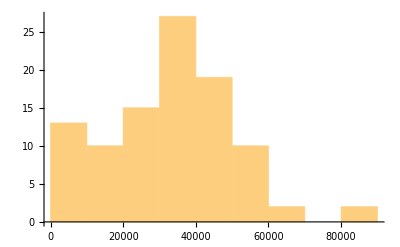

```mathematica
ds[Histogram,"amount"]
```

```mathematica
byPrice=ds[ReverseSortBy[#amount&]]
```

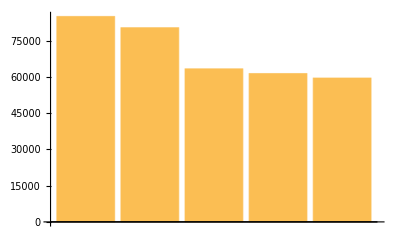

```mathematica
byPrice[[1;;5]][BarChart,"amount"]
```

```mathematica
EntityUnregister[store]
```

```mathematica
data=SemanticImport["ExampleData/TreesOwnedByTheCityOfChampaign.csv"]
```

Dataset[<>]

```mathematica
data[Counts,"Number of Trunks"]
```

```mathematica
data[MaximalBy["Number of Trunks"]]
```

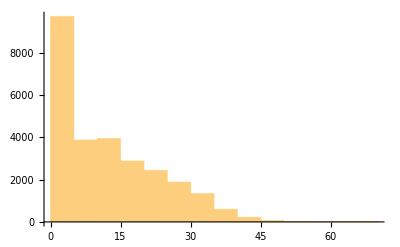

```mathematica
data[Histogram,3]
```

```mathematica
N[data[Mean,3]]
```

11.7869

```mathematica
data[DeleteDuplicates,"Tree Species"]
```

```mathematica
data[TakeLargestBy["Diameter at Breast Height (in Feet)",10],"Location"]
```

```mathematica
GeoGraphics[GeoMarker[data[TakeLargestBy["Diameter at Breast Height (in Feet)",10],"Location"]]]
```

-Graphics-